```mathematica
Import["resources/jojon.edn"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
Import["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/logs/pre-pengumuman-sbmptn-in-parent-filtered-sma.edn"]
```

[{:datum {42 1}, :memberid 184446, :class :sma, :subclass :sma11KTSP, :maxi 1, :total 1} {:datum {639 85, 41 48, 43 41, 45 169, 42 48}, :memberid 221885, :class :sma, :subclass :s…P, :maxi 3, :total 6} {:datum {627 2, 182 7, 22 83, 41 26, 43 2, 25 3, 11 779, 45 956, 10 56, 8 2}, :memberid 211523, :class :sma, :subclass :sma12Alumni, :maxi 956, :total 1916}]
 |  |  |  |

```mathematica
Import["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/logs/presbmptn.json"]
```

{{subclass→sma12Alumni,class→sma,memberid→221885,datum→{45→169,639→85,41→48,43→41,42→48},maxi→169,total→391},16162,{subclass→sma12Alumni,class→sma,memberid→211523,datum→{10→56,45→956,182→7,627→2,43→2,22→83,41→26,25→3,11→779,8→2},maxi→956,total→1916}}
 |  |  |  |

```mathematica
Dimensions[%3]
```

{16164,6}

```mathematica
TableForm[%3⟦All,All,2⟧,TableHeadings->{None,%3⟦1,All,1⟧}]
```

1
 |  |  |  |

```mathematica
"subclass"/.%3
```

{sma12Alumni,sma12Alumni,sma10KTSP,sma12Alumni,sma10KTSP,sma12Alumni,sma12Alumni,sma12Alumni,sma12UN,sma12Alumni,sma12Alumni,sma12Alumni,sma12Alumni,sma12UN,16137,sma12Alumni,sma10K13,sma10KTSP,sma10K13,sma12Alumni,sma12Alumni,sma10K13,sma11KTSP,sma10KTSP,sma12UN,sma11KTSP,sma12Alumni,sma12Alumni}
 |  |  |  |

```mathematica
Tally[%9]
```

{{sma12Alumni,9148},{sma10KTSP,1361},{sma12UN,2883},{sma11KTSP,1070},{sma11K13,977},{sma10K13,725}}

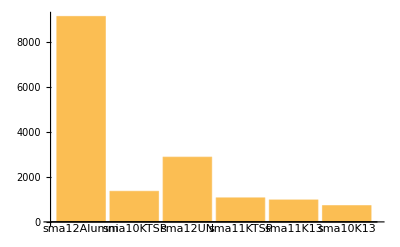

```mathematica
BarChart[Apply[Labeled,Reverse[{{"sma12Alumni",9148},{"sma10KTSP",1361},{"sma12UN",2883},{"sma11KTSP",1070},{"sma11K13",977},{"sma10K13",725}},2],{1}]]
```

```mathematica
PieChart[Apply[Labeled,Reverse[{{"sma12Alumni",9148},{"sma10KTSP",1361},{"sma12UN",2883},{"sma11KTSP",1070},{"sma11K13",977},{"sma10K13",725}},2],{1}]]
```

-Graphics-

```mathematica
"maxi"/.%3
```

{169,141,623,658,59,186,317,772,49,413,482,70,678,117,90,135,72,384,899,2636,198,417,390,719,1075,421,78,3479,144,619,139,398,1775,174,152,825,91,65,275,183,476,452,283,142,83,425,16072,207,127,38,587,73,493,129,1292,291,318,350,839,502,1258,59,327,117,70,458,59,86,60,912,390,137,895,481,321,127,12,122,194,374,94,620,99,806,458,148,172,288,124,43,53,245,956}
 |  |  |  |

```mathematica
"datum"/.%3
```

{{45→169,639→85,41→48,43→41,42→48},{43→5,45→141,11→31,22→4,638→31},{41→623,45→4,639→118,44→1},{45→658,43→72},{41→59},16155,{43→43,42→1,41→31,44→8},{42→53,23→31,638→8,22→15,41→5},{45→245},{10→56,45→956,182→7,627→2,43→2,22→83,41→26,25→3,11→779,8→2}}
 |  |  |  |

```mathematica
Dimensions[%5]
```

{16164}

```mathematica
Times@@{16164}
```

16164

```mathematica
"total"/.%3
```

{391,212,746,730,59,218,318,772,83,528,489,81,711,117,91,140,95,810,1916,2705,425,448,748,1968,1078,533,78,4880,240,619,215,398,2072,505,386,1234,92,66,466,338,531,468,283,189,83,16074,194,109,1166,82,493,358,1527,291,823,350,842,956,1952,59,327,117,70,501,134,86,173,917,432,137,1499,604,351,178,65,235,285,401,140,801,221,1293,604,153,175,689,494,83,112,245,1916}
 |  |  |  |

```mathematica
pers = x^5 + x^3 + 10
```

10+x^3+x^5

```mathematica
D[pers,x]
```

3 x^2+5 x^4

```mathematica
Integrate[pers,x]
```

10 x+x^4/4+x^6/6

```mathematica
Integrate[pers,y]
```

(10+x^3+x^5) y

```mathematica
tur = D[pers,x]
```

3 x^2+5 x^4

```mathematica
D[pers,y]
```

0

```mathematica
Table[tur[i], {i,1,10}]
```

{(3 x^2+5 x^4)[1],(3 x^2+5 x^4)[2],(3 x^2+5 x^4)[3],(3 x^2+5 x^4)[4],(3 x^2+5 x^4)[5],(3 x^2+5 x^4)[6],(3 x^2+5 x^4)[7],(3 x^2+5 x^4)[8],(3 x^2+5 x^4)[9],(3 x^2+5 x^4)[10]}

```mathematica
tur[1]
```

(3 x^2+5 x^4)[1]

```mathematica
tur[1]//N
```

(3. x^2+5. x^4)[1.]

```mathematica
N//tur[1]
```

(3 x^2+5 x^4)[1][N]

```mathematica
Import["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/logs/mat-class-snmptn.json"]
```

{{lulus→True,total→67,maxi→67},{lulus→False,total→83,maxi→49},{lulus→True,total→116,maxi→71},{lulus→False,total→117,maxi→117},{lulus→False,total→425,maxi→198},3658,{lulus→True,total→672,maxi→318},{lulus→True,total→740,maxi→574},{lulus→False,total→178,maxi→127},{lulus→False,total→83,maxi→43}}
 |  |  |  |

```mathematica
data = %
```

{{lulus→True,total→67,maxi→67},{lulus→False,total→83,maxi→49},{lulus→True,total→116,maxi→71},{lulus→False,total→117,maxi→117},{lulus→False,total→425,maxi→198},3658,{lulus→True,total→672,maxi→318},{lulus→True,total→740,maxi→574},{lulus→False,total→178,maxi→127},{lulus→False,total→83,maxi→43}}
 |  |  |  |

```mathematica
Plot[data]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[data]

```mathematica
ListPlot[data]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{{lulus→True,total→67,maxi→67},{lulus→False,total→83,maxi→49},{lulus→True,total→116,maxi→71},{lulus→False,total→117,maxi→117},3659,{lulus→True,total→672,maxi→318},{lulus→True,total→740,maxi→574},{lulus→False,total→178,maxi→127},{lulus→False,total→83,maxi→43}}]
 |  |  |  |

```mathematica
data
```

{{lulus→True,total→67,maxi→67},{lulus→False,total→83,maxi→49},{lulus→True,total→116,maxi→71},{lulus→False,total→117,maxi→117},{lulus→False,total→425,maxi→198},3658,{lulus→True,total→672,maxi→318},{lulus→True,total→740,maxi→574},{lulus→False,total→178,maxi→127},{lulus→False,total→83,maxi→43}}
 |  |  |  |

```mathematica
por = <| x -> 60 , y -> 10|>
```

<|x→60,y→10|>

```mathematica
por[[x]]
```

Part::pkspec1: The expression x cannot be used as a part specification.

<|x→60,y→10|>⟦x⟧

```mathematica
por.x
```

<|x→60,y→10|>.x

```mathematica
data1 = Map[<| lulus -> Lookup[#,"lulus"], datum -> {Lookup[#,"maxi"],Lookup[#,"total"]}|>&,data]
```

{<|lulus→True,datum→{67,67}|>,<|lulus→False,datum→{49,83}|>,<|lulus→True,datum→{71,116}|>,<|lulus→False,datum→{117,117}|>,<|lulus→False,datum→{198,425}|>,<|lulus→False,datum→{390,748}|>,3656,<|lulus→True,datum→{198,277}|>,<|lulus→True,datum→{318,672}|>,<|lulus→True,datum→{574,740}|>,<|lulus→False,datum→{127,178}|>,<|lulus→False,datum→{43,83}|>}
 |  |  |  |

```mathematica
data1a = Map[Lookup[#,datum]&,Select[data1, Lookup[#,lulus] == True&]]
```

{{67,67},{71,116},{719,1924},{119,191},{947,1233},{1170,3838},{324,554},{302,604},{3018,4997},{158,391},{592,1278},{168,389},{195,229},{398,504},{59,66},{237,249},{551,731},{303,635},{377,1085},{1063,2917},{118,285},{500,1136},{491,519},{447,1121},{53,109},{274,564},{521,1467},{1095,2097},{467,692},{241,543},{250,485},{279,432},{190,717},{1200,2673},{298,427},{410,731},{117,129},{51,137},{219,358},{2065,4606},{284,619},{1065,2641},{233,455},{133,164},{618,632},{70,200},{148,202},{390,780},{755,1040},{290,578},{129,136},{2220,4377},{381,1087},{277,620},{2438,4545},{716,1739},{281,378},{416,595},{731,1083},{452,1213},{349,772},{54,241},{234,750},{2195,3629},{75,104},{48,136},{445,570},{363,670},{634,982},{2252,2459},{458,1060},{711,1161},{640,1047},{560,1839},{866,2038},{285,507},{233,337},{1113,2065},{931,2706},{318,779},{310,444},{88,156},{223,257},{380,677},{132,274},{603,836},{1931,2940},{496,1489},{1162,1566},{293,641},{276,747},{169,369},{199,199},{216,445},{50,52},{1352,2541},{132,216},{443,960},{1675,4773},{1302,2440},{72,113},{787,1544},{948,2748},{688,2040},{334,749},{252,648},{738,1397},{1193,2831},{923,2351},{38,68},{301,825},{22,56},{1240,2010},{2000,4903},{716,1099},{46,88},{895,1653},{703,949},{159,291},{1431,2575},{339,803},{1155,3192},{639,991},{1354,3173},{233,372},{636,1241},{982,2031},{277,867},{255,477},{340,841},{250,837},{721,2967},{640,1199},{915,2923},{229,423},{553,986},{887,1981},{145,272},{645,1289},{273,530},{279,760},{310,467},{73,97},{308,423},{775,1494},{33,70},{827,1571},{495,830},{80,80},{663,2027},{472,660},{115,152},{42,52},{116,174},{239,412},{1304,3754},{266,433},{959,2703},{110,360},{175,285},{159,330},{733,2123},{254,297},{89,291},{49,51},{160,370},{285,625},{2118,3492},{1223,3102},{1155,2423},{963,1123},{318,606},{725,1437},{143,372},{533,1516},{302,627},{459,984},{83,87},{278,339},{46,84},{1959,4017},{54,71},{1754,1914},{369,724},{1116,2515},{237,351},{764,1550},{2873,3506},{302,1052},{492,514},{476,1202},{414,754},{250,590},{288,453},{274,333},{1144,3189},{292,680},{105,363},{108,309},{1525,1903},{321,638},{1856,2882},{89,137},{216,415},{77,179},{102,223},{364,621},{385,1037},{688,1135},{223,623},{421,768},{945,1935},{477,647},{129,449},{593,935},{236,554},{1853,3456},{133,265},{62,170},{1053,2776},{42,77},{102,102},{78,232},{397,493},{737,1324},{123,123},{360,834},{459,1573},{1482,1938},{687,1335},{221,270},{70,125},{97,334},{183,427},{378,1083},{665,1237},{434,877},{1960,4502},{1068,2017},{224,538},{76,203},{34,63},{108,215},{56,121},{683,1009},{59,109},{51,109},{1700,3746},{1609,2490},{287,348},{1019,1601},{991,1271},{688,823},{123,249},{360,971},{203,207},{785,1346},{767,769},{938,2101},{393,445},{699,1121},{282,590},{594,1159},{681,1737},{231,329},{699,1301},{642,877},{115,257},{662,1892},{347,400},{801,2647},{690,1476},{566,1908},{440,578},{1792,2702},{438,498},{162,369},{128,143},{470,735},{2188,4755},{504,1194},{553,1295},{259,745},{302,1026},{64,115},{432,713},{187,285},{257,462},{389,1345},{809,2406},{763,926},{56,58},{612,861},{457,534},{534,1198},{679,1860},{970,1397},{336,725},{29,68},{332,792},{458,1380},{128,252},{446,579},{645,1274},{488,2227},{603,639},{574,956},{1225,2031},{450,663},{377,845},{311,737},{301,964},{914,1705},{415,945},{255,678},{886,1399},{388,640},{855,1814},{110,228},{2162,3330},{753,1216},{614,1106},{101,316},{608,1957},{759,2271},{110,274},{100,120},{79,107},{130,263},{267,545},{431,1038},{311,432},{210,211},{470,1310},{395,996},{1157,3560},{414,811},{449,1529},{799,2174},{887,2172},{73,79},{862,895},{172,288},{327,891},{755,1062},{127,130},{1088,4259},{480,2218},{797,1566},{302,1103},{233,384},{236,957},{391,996},{1105,2017},{763,2168},{112,226},{450,840},{533,1487},{358,717},{132,301},{97,222},{1114,1939},{644,1022},{94,172},{286,542},{527,906},{710,1352},{450,967},{71,282},{117,271},{532,568},{230,356},{68,167},{312,518},{233,565},{567,1478},{213,271},{2302,4973},{358,717},{993,1991},{338,425},{61,61},{216,384},{455,1238},{212,215},{46,79},{242,303},{939,1957},{853,859},{469,866},{1119,3472},{96,98},{324,740},{193,506},{110,302},{41,75},{238,476},{984,2578},{63,100},{66,70},{351,883},{487,812},{249,401},{422,1303},{80,116},{43,94},{75,133},{1580,3338},{57,124},{263,440},{591,906},{271,300},{166,278},{608,1508},{281,389},{98,141},{1260,2187},{115,242},{249,712},{343,353},{751,1642},{454,698},{1523,3354},{577,1771},{1767,3257},{557,999},{510,940},{421,810},{73,211},{260,593},{1589,1958},{57,61},{238,423},{161,294},{887,2368},{1796,3969},{1650,2465},{404,696},{283,1084},{102,376},{830,2170},{43,119},{189,315},{30,54},{120,202},{872,1766},{378,799},{573,1681},{76,82},{516,541},{372,373},{169,563},{524,914},{1488,1907},{281,543},{492,1421},{127,212},{375,916},{168,614},{369,369},{177,351},{450,1181},{349,669},{558,941},{88,146},{1095,3287},{163,231},{59,112},{188,300},{1673,3833},{1179,2387},{253,279},{538,3021},{91,264},{717,1170},{57,101},{230,415},{48,58},{1328,2294},{333,684},{415,995},{188,269},{37,110},{331,560},{297,730},{233,422},{340,476},{264,506},{560,1192},{484,543},{57,175},{172,409},{103,208},{460,570},{1417,3811},{49,113},{924,1534},{61,61},{570,1517},{403,1184},{297,937},{147,207},{370,472},{97,238},{584,1140},{130,267},{2757,4703},{185,313},{566,1595},{235,466},{223,389},{489,1602},{118,318},{67,112},{281,558},{105,165},{373,524},{207,288},{2036,4273},{259,453},{192,499},{1600,3550},{344,691},{236,491},{542,1014},{651,1258},{381,962},{574,1083},{42,85},{378,951},{107,182},{112,148},{323,356},{315,750},{426,554},{800,1941},{1202,1616},{37,52},{467,889},{411,1149},{1020,1757},{164,243},{176,183},{936,1031},{178,424},{659,1971},{1835,3908},{82,107},{266,441},{200,278},{381,641},{102,201},{193,240},{131,400},{230,653},{527,876},{764,1095},{183,500},{269,654},{693,1112},{639,907},{87,127},{1654,4633},{456,1094},{126,126},{194,270},{307,402},{126,208},{241,286},{2100,2968},{276,414},{158,240},{303,485},{272,291},{233,396},{154,221},{683,1084},{192,230},{495,1112},{109,118},{192,209},{318,686},{347,540},{149,223},{240,857},{335,873},{146,332},{445,834},{370,535},{228,259},{28,64},{189,430},{563,1234},{104,247},{1227,2628},{1354,3974},{366,1142},{829,1550},{1069,1984},{407,1253},{234,441},{841,2070},{44,90},{504,973},{594,1854},{87,187},{172,179},{814,1436},{765,1155},{62,66},{202,574},{304,923},{1561,2199},{474,753},{969,2174},{253,544},{1373,2874},{1120,2345},{437,645},{2171,3357},{37,62},{723,1886},{118,176},{350,745},{751,1689},{149,222},{920,1113},{310,726},{1530,2976},{1154,1377},{211,302},{1656,3035},{2196,3853},{170,319},{115,115},{235,543},{848,1445},{585,723},{212,299},{205,246},{308,579},{1345,3584},{255,348},{189,298},{262,449},{420,965},{319,895},{967,1279},{198,375},{343,834},{370,449},{510,1098},{140,205},{370,854},{959,3571},{135,193},{489,573},{838,2078},{1267,3201},{323,1145},{125,220},{191,253},{347,716},{213,283},{110,213},{1889,4007},{857,1777},{229,320},{590,1879},{624,1137},{106,178},{399,1152},{192,307},{348,391},{588,2271},{636,1211},{53,101},{37,57},{34,51},{343,604},{236,709},{1773,3420},{441,855},{276,547},{323,323},{164,654},{911,1143},{875,2088},{349,475},{558,2398},{126,218},{290,527},{94,346},{392,849},{385,818},{119,383},{67,113},{272,374},{565,877},{771,2329},{1925,2649},{2189,3417},{2227,4434},{867,1114},{912,1770},{729,1280},{901,1969},{78,144},{58,129},{318,774},{375,530},{198,497},{360,971},{362,588},{1008,2939},{2128,3189},{391,518},{24,67},{1147,2243},{239,644},{1165,2442},{250,684},{480,1210},{241,640},{188,308},{438,738},{281,493},{440,931},{192,380},{195,390},{1505,4121},{1647,3505},{59,203},{1111,1801},{349,462},{2580,3818},{103,103},{340,462},{936,2076},{344,550},{209,800},{466,1249},{704,1572},{174,242},{536,846},{597,1946},{955,1543},{1959,3287},{113,184},{735,1069},{513,681},{496,823},{403,1130},{316,493},{138,138},{280,508},{775,2385},{376,557},{82,110},{1068,1907},{973,1363},{638,1435},{356,549},{71,242},{330,937},{718,1834},{706,1126},{533,1170},{114,290},{56,151},{570,1113},{495,667},{668,1100},{460,768},{54,54},{2362,2920},{144,180},{344,428},{143,185},{147,224},{660,1365},{352,610},{610,716},{140,233},{1171,2446},{2219,4505},{381,431},{188,784},{130,291},{81,227},{801,1618},{560,847},{221,287},{87,198},{193,278},{1818,3443},{600,813},{340,496},{966,3197},{265,327},{284,861},{426,761},{738,889},{166,385},{1173,1273},{517,1053},{1262,2433},{160,209},{909,1124},{163,461},{254,258},{192,664},{357,678},{188,190},{2254,4070},{906,2359},{1878,4019},{188,651},{278,357},{1264,1588},{317,827},{89,97},{447,829},{418,1066},{127,128},{1381,2903},{630,752},{823,1209},{352,853},{140,394},{86,142},{198,220},{784,1084},{84,210},{544,579},{408,1198},{351,355},{1364,2471},{533,1233},{230,296},{190,199},{920,1251},{1346,2043},{308,685},{86,298},{349,355},{810,905},{148,291},{764,2301},{327,672},{68,151},{673,1254},{360,649},{1684,1819},{106,137},{534,842},{155,340},{665,1272},{316,603},{245,721},{197,435},{827,1773},{755,1797},{252,964},{89,150},{1005,2304},{1383,2129},{205,397},{970,2666},{108,139},{1211,1292},{118,374},{282,344},{1865,2723},{229,273},{131,160},{256,317},{393,445},{158,193},{1891,2257},{622,768},{639,732},{167,328},{1714,4701},{306,843},{485,1049},{145,388},{120,139},{1091,3346},{966,2648},{399,1130},{950,2297},{74,176},{57,99},{3068,3705},{429,507},{179,340},{239,630},{194,372},{175,491},{873,2024},{966,1870},{426,784},{59,83},{400,584},{136,192},{29,58},{148,298},{39,77},{592,1244},{151,459},{493,1460},{1420,2385},{694,1306},{366,422},{591,1195},{34,71},{272,932},{263,370},{557,1739},{345,891},{127,214},{590,690},{119,265},{261,287},{472,847},{1057,1699},{1048,1495},{825,2018},{138,268},{278,400},{85,152},{845,1125},{1154,2587},{21,55},{610,1246},{606,1075},{367,973},{121,433},{604,1387},{233,426},{792,1765},{490,787},{184,405},{111,169},{100,147},{335,763},{245,498},{538,904},{285,541},{694,1466},{131,220},{178,383},{656,1299},{79,134},{120,328},{298,674},{106,120},{549,696},{483,1247},{607,1589},{477,833},{1153,1698},{172,289},{68,76},{555,1365},{278,493},{152,375},{162,298},{648,1838},{155,292},{476,1329},{270,598},{498,534},{174,618},{241,524},{142,256},{2142,3600},{1402,3178},{436,951},{86,135},{338,861},{773,1512},{903,1319},{417,1347},{310,802},{506,1491},{214,305},{180,187},{1352,4200},{1079,1448},{1003,2211},{45,132},{765,1936},{840,849},{1152,2481},{2073,4852},{169,219},{360,497},{22,61},{152,198},{273,670},{1313,1687},{1093,1476},{113,186},{205,442},{270,303},{1657,3311},{933,2673},{698,1044},{2345,3795},{615,1803},{248,372},{67,67},{67,85},{227,325},{972,1150},{691,1010},{411,634},{81,84},{317,386},{676,1431},{413,677},{664,1673},{851,1230},{450,1462},{139,460},{282,854},{579,1280},{359,652},{1088,2033},{924,1897},{473,885},{1424,2620},{963,970},{104,180},{1192,3242},{1369,1369},{91,302},{72,171},{269,480},{320,675},{534,826},{1847,3438},{791,2242},{470,743},{776,2150},{817,2567},{92,283},{1073,1644},{365,875},{788,2273},{177,273},{134,175},{76,104},{329,724},{44,67},{139,266},{1271,2058},{248,521},{316,602},{1577,4990},{629,1648},{321,522},{986,1682},{534,1572},{61,158},{303,998},{298,723},{303,562},{263,417},{506,613},{188,436},{231,568},{164,295},{292,505},{286,583},{196,452},{356,1491},{683,1464},{29,82},{336,860},{330,399},{2371,3694},{2047,3588},{788,999},{1298,3254},{703,1642},{60,113},{259,563},{179,364},{198,320},{1434,3926},{187,242},{1892,3239},{323,659},{413,590},{471,723},{1719,4197},{268,348},{546,578},{26,54},{351,455},{1412,3699},{314,635},{434,604},{1390,3288},{105,173},{224,623},{66,93},{63,115},{96,252},{107,134},{372,982},{1002,2626},{166,449},{503,1092},{283,514},{924,930},{106,106},{1143,2946},{52,105},{1086,3439},{343,443},{69,74},{146,392},{266,537},{149,447},{501,580},{637,1318},{164,258},{2415,2644},{394,491},{261,776},{2115,2779},{80,110},{289,397},{682,1515},{137,210},{205,262},{650,1129},{786,1528},{1867,2982},{524,1167},{407,903},{152,403},{215,504},{241,434},{73,108},{253,712},{207,500},{355,712},{45,51},{228,239},{277,971},{443,697},{162,177},{767,1209},{480,1061},{2288,3516},{159,434},{508,937},{85,99},{418,968},{722,1289},{1405,2443},{1285,3640},{1161,2196},{299,685},{862,2015},{215,335},{390,710},{89,163},{514,1058},{1051,2230},{586,800},{212,414},{605,1155},{1447,2779},{342,1131},{108,333},{231,240},{506,1224},{733,1998},{209,607},{221,520},{989,1940},{277,386},{54,57},{640,2019},{1521,3131},{45,79},{92,234},{498,1100},{295,594},{918,3004},{1056,1347},{1286,2469},{756,871},{838,1854},{1040,2132},{551,691},{658,1441},{359,1163},{102,176},{481,1100},{2553,4797},{332,341},{128,157},{1011,1578},{130,224},{305,449},{537,1833},{146,162},{167,168},{148,405},{53,55},{201,407},{213,466},{653,1396},{209,231},{67,106},{403,794},{653,1711},{28,68},{41,61},{678,1360},{294,522},{161,426},{909,2061},{1262,1622},{57,104},{1136,1964},{73,99},{332,718},{159,233},{1041,3174},{851,2248},{122,273},{735,1267},{1593,2819},{619,1112},{1040,2420},{130,139},{2699,3589},{84,130},{586,2649},{1335,1946},{343,732},{521,818},{588,1973},{69,93},{699,2321},{439,960},{587,918},{871,2211},{321,508},{299,860},{483,899},{229,492},{742,1260},{46,59},{421,1249},{1218,2689},{902,1646},{145,274},{359,1013},{102,230},{521,668},{682,774},{289,743},{46,82},{94,187},{974,1442},{713,1666},{246,576},{279,502},{79,97},{395,799},{815,1283},{652,1211},{910,1890},{33,53},{457,1343},{86,109},{348,518},{1055,1746},{626,1182},{141,462},{248,289},{165,321},{238,399},{350,685},{1134,1521},{259,379},{359,456},{253,497},{319,1108},{486,1321},{208,695},{276,457},{117,128},{205,454},{333,625},{303,506},{1023,1997},{139,482},{811,992},{262,486},{2303,4450},{36,74},{386,638},{117,236},{575,1447},{204,565},{1292,2179},{272,758},{278,381},{330,766},{155,203},{60,151},{117,149},{367,1134},{977,4383},{396,753},{293,1068},{38,52},{116,202},{380,896},{272,733},{1341,2039},{60,98},{66,97},{127,192},{342,795},{1168,1843},{903,2281},{202,347},{2106,3585},{116,149},{887,1961},{51,95},{161,252},{245,568},{973,2172},{298,394},{31,54},{1349,1944},{384,921},{377,543},{208,505},{486,739},{66,118},{158,366},{100,251},{63,148},{89,89},{1751,2263},{824,893},{90,140},{282,872},{790,1864},{96,240},{496,675},{448,1577},{360,481},{102,102},{906,1997},{608,1146},{282,394},{175,293},{1365,2954},{1551,3144},{168,271},{192,282},{197,267},{460,949},{1292,2945},{130,308},{1767,2542},{764,1305},{309,805},{1147,3777},{237,327},{248,331},{478,825},{274,984},{485,1061},{532,1092},{1247,1441},{68,239},{45,109},{754,1927},{637,1084},{698,1943},{218,339},{329,537},{135,221},{2715,3769},{464,550},{901,1494},{870,1252},{785,2447},{61,102},{300,511},{356,1497},{203,411},{156,421},{134,408},{999,1956},{1272,2666},{308,517},{1658,2013},{1086,2037},{107,144},{632,891},{538,1374},{1147,1904},{60,61},{384,667},{659,1576},{816,860},{622,1067},{185,230},{56,130},{505,1178},{330,707},{298,380},{301,321},{47,100},{430,610},{53,53},{490,1174},{82,134},{270,388},{413,792},{1209,3050},{93,205},{837,1236},{1234,1834},{527,571},{981,1409},{267,478},{84,84},{259,541},{363,1371},{747,780},{960,2108},{54,54},{714,1136},{1223,1738},{868,1562},{744,1577},{93,128},{484,1674},{485,1323},{578,1057},{697,1413},{512,625},{482,733},{344,573},{538,860},{799,2267},{243,350},{1592,4813},{169,502},{1337,3985},{631,1634},{820,2815},{31,109},{330,779},{193,193},{739,1458},{676,1788},{871,2580},{591,1384},{166,255},{1552,2904},{105,327},{172,407},{66,215},{346,623},{451,1184},{247,318},{663,1064},{1239,3432},{43,165},{192,829},{865,1623},{205,407},{306,734},{636,1094},{82,220},{75,104},{403,486},{123,149},{100,153},{73,113},{398,541},{1138,2457},{67,290},{254,529},{488,803},{29,75},{201,293},{540,1255},{109,257},{41,102},{1684,2305},{217,421},{276,521},{966,1446},{542,1597},{744,1096},{302,663},{48,97},{400,620},{381,763},{460,1295},{733,1539},{359,845},{133,221},{71,95},{444,856},{743,1146},{121,282},{204,288},{319,668},{123,435},{409,409},{831,1512},{1116,1825},{525,731},{652,1635},{385,1247},{575,655},{225,305},{73,213},{320,431},{491,837},{113,155},{285,613},{2784,3557},{1338,4440},{1836,3724},{1195,2334},{100,279},{891,2918},{248,711},{1149,2363},{262,434},{991,1664},{389,634},{1404,3438},{95,152},{183,185},{1280,3219},{142,338},{310,360},{1121,2507},{716,2319},{59,80},{206,655},{846,1983},{182,417},{505,701},{573,809},{2152,3935},{1046,2321},{1279,2640},{47,109},{1037,2285},{204,282},{177,309},{1506,2201},{925,1447},{1128,2256},{940,1226},{385,915},{390,1067},{790,1232},{652,1554},{2193,4814},{134,261},{1798,2872},{324,343},{70,122},{348,403},{183,330},{781,1588},{164,262},{560,1572},{112,156},{337,797},{1249,2782},{142,151},{174,561},{171,222},{570,825},{199,305},{475,923},{392,1374},{1174,2233},{224,451},{35,77},{146,311},{350,849},{128,435},{1130,2255},{1512,2800},{68,77},{490,1485},{632,1252},{674,1282},{631,939},{91,116},{1611,3319},{426,1223},{973,1755},{83,214},{224,380},{493,600},{1058,2175},{136,225},{1086,1614},{536,1661},{781,1536},{55,89},{229,337},{106,221},{635,1712},{211,433},{373,596},{567,1022},{609,1003},{984,1294},{489,1004},{502,968},{1258,3131},{221,310},{83,106},{557,704},{1152,2662},{481,921},{315,922},{102,111},{364,773},{440,583},{87,137},{468,991},{494,1019},{1239,4312},{176,308},{81,83},{618,1286},{818,1508},{324,730},{1275,4334},{505,636},{216,431},{586,608},{329,376},{177,289},{312,367},{789,882},{113,243},{40,122},{558,645},{329,884},{790,1362},{447,898},{77,195},{240,688},{789,1470},{104,192},{228,383},{733,812},{160,285},{723,1016},{194,351},{1007,2076},{382,899},{750,1548},{134,376},{53,53},{564,1335},{511,905},{750,1092},{209,587},{1172,2150},{516,984},{179,226},{302,377},{160,207},{869,1205},{707,1011},{167,348},{116,224},{179,196},{127,322},{711,1658},{267,457},{398,603},{618,1465},{773,1080},{936,1795},{611,1927},{313,395},{347,351},{322,625},{395,944},{100,171},{270,692},{1380,3061},{1787,2187},{1520,3144},{97,137},{79,143},{213,637},{111,394},{299,537},{1282,2121},{1970,3677},{700,1361},{448,560},{265,628},{1099,4182},{110,211},{46,109},{507,550},{453,1176},{202,235},{1935,4306},{273,380},{471,1718},{699,1442},{514,879},{890,1872},{223,290},{68,68},{106,106},{85,178},{3222,4764},{320,840},{121,368},{746,1224},{1124,1738},{478,1002},{650,911},{1850,4634},{174,347},{108,138},{121,207},{230,385},{279,410},{166,305},{152,167},{512,1051},{340,541},{178,181},{76,95},{1464,2754},{47,92},{266,365},{96,283},{141,433},{477,848},{602,1240},{102,177},{283,847},{76,125},{2125,4143},{576,1209},{285,937},{130,173},{249,487},{988,2353},{386,582},{676,2200},{2138,4713},{903,903},{1661,1818},{2661,4282},{919,1597},{1213,1949},{203,521},{89,138},{505,617},{115,186},{1507,1806},{333,810},{206,263},{77,197},{1000,2320},{466,701},{46,123},{205,266},{159,174},{1385,2898},{69,166},{805,2138},{76,88},{214,359},{1016,2623},{1911,4301},{172,299},{333,911},{72,104},{712,1130},{955,1693},{889,2147},{980,2519},{1210,3518},{166,445},{105,135},{554,1428},{582,621},{459,1054},{268,521},{554,627},{798,1373},{681,1448},{134,160},{300,439},{179,237},{94,199},{292,421},{1383,2243},{151,409},{1464,2001},{525,904},{478,607},{423,1567},{175,538},{208,414},{305,478},{157,218},{2152,4365},{539,775},{212,246},{625,716},{411,812},{142,274},{988,2246},{920,1693},{515,959},{198,277},{318,672},{574,740}}

```mathematica
data1b = Map[Lookup[#,datum] &, Select[data1,Lookup[#,lulus] == False &]];
```

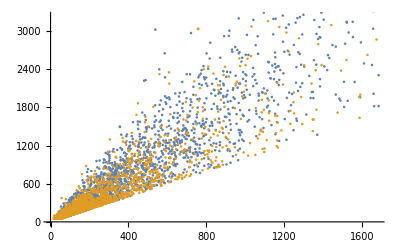

```mathematica
ListPlot[{data1a,data1b}]
```

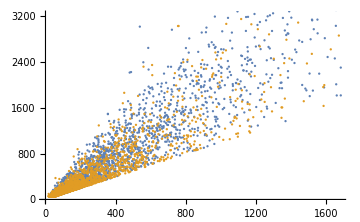

```mathematica
Show[%37,ImageSize->Medium]
```

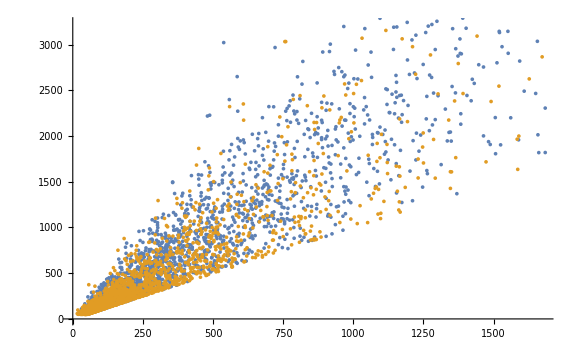

```mathematica
Show[%39,ImageSize->Large]
```

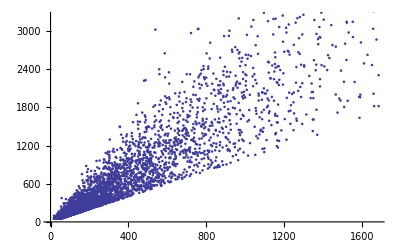

```mathematica
ListPlot[{data1a,data1b},PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[1.0050000000000001]]]
```

```mathematica
ListPlot
```

```mathematica
sbmptn = Import["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/logs/mat-class-sbmptn.json"]
```

{{lulus→False,maxi→169,total→391},{lulus→False,maxi→141,total→212},{lulus→False,maxi→658,total→730},{lulus→False,maxi→186,total→218},8391,{lulus→True,maxi→458,total→604},{lulus→False,maxi→148,total→153},{lulus→False,maxi→245,total→245},{lulus→False,maxi→956,total→1916}}
 |  |  |  |

```mathematica
sbmptn1 = Map[<| lulus -> Lookup[#,"lulus"], datum -> {Lookup[#,"maxi"],Lookup[#,"total"]}|>&, sbmptn]
```

{<|lulus→False,datum→{169,391}|>,<|lulus→False,datum→{141,212}|>,<|lulus→False,datum→{658,730}|>,<|lulus→False,datum→{186,218}|>,<|lulus→False,datum→{317,318}|>,<|lulus→False,datum→{772,772}|>,8388,<|lulus→False,datum→{94,140}|>,<|lulus→True,datum→{458,604}|>,<|lulus→False,datum→{148,153}|>,<|lulus→False,datum→{245,245}|>,<|lulus→False,datum→{956,1916}|>}
 |  |  |  |

```mathematica
sbmptn1a = Map[Lookup[#,datum]&, Select[sbmptn1, Lookup[#,lulus] == True&]]
```

{{1075,1078},{3479,4880},{918,1933},{3400,8573},{4491,6945},{186,503},{258,505},{922,922},{359,366},{356,617},{468,468},{928,935},{4923,6324},{9086,9860},{1031,1048},{87,186},{1483,2532},{587,1659},{3436,7170},{3100,4219},{997,1969},{3095,3545},{2941,3148},{4053,6221},{404,604},{1327,1350},{1287,1287},{860,1445},{613,619},{622,651},{2266,2726},{352,352},{183,393},{4936,8307},{3489,5159},{218,242},{2643,2848},{392,865},{1369,1398},{5550,7713},{2556,3185},{376,920},{493,836},{1023,1023},{365,725},{518,575},{558,561},{3610,8708},{778,778},{511,1503},{610,738},{1793,3441},{361,361},{768,833},{634,634},{4619,7264},{232,239},{1168,1185},{649,649},{2268,2271},{939,939},{4089,4818},{382,387},{497,1009},{1033,1041},{408,415},{970,981},{1428,1546},{1889,3076},{5032,8133},{5148,5421},{1614,1729},{447,481},{965,984},{511,932},{85,107},{1789,1986},{1765,1820},{1072,1072},{3229,3231},{999,1439},{8794,8823},{974,1439},{2079,7511},{939,939},{534,769},{497,562},{751,758},{203,203},{880,1727},{848,1184},{2975,2985},{938,2385},{524,693},{207,313},{2912,2949},{1025,1272},{1615,3595},{93,206},{2529,5308},{124,124},{893,893},{1395,2472},{696,697},{2422,2487},{352,1025},{65,127},{181,181},{832,2698},{485,1680},{2521,2777},{1353,1573},{3899,6309},{630,1405},{2574,4478},{1784,2013},{388,782},{422,483},{248,758},{365,933},{1229,2505},{1249,1338},{704,773},{2348,5098},{2143,2327},{4939,6333},{3027,3764},{1114,2819},{1740,2053},{4348,5533},{924,2006},{2383,5619},{1184,2456},{1074,1668},{318,319},{1944,3382},{914,1024},{130,134},{305,635},{7629,7629},{244,331},{765,939},{590,796},{788,1354},{1715,4290},{3210,3549},{3736,3961},{149,233},{134,134},{804,1278},{244,390},{996,1058},{2065,4320},{1717,3255},{3979,4283},{413,545},{164,277},{1490,4347},{763,855},{816,869},{1496,1616},{418,679},{699,966},{731,811},{530,665},{1403,1542},{419,554},{941,2017},{97,242},{403,403},{131,167},{760,762},{6439,7903},{1593,1651},{2973,4569},{366,522},{921,1061},{1509,1779},{849,1195},{2133,2329},{106,220},{175,193},{1030,2648},{733,733},{252,290},{1437,1466},{4696,6416},{2364,7318},{1777,1777},{99,138},{977,985},{1603,2882},{720,721},{2318,2422},{355,857},{914,923},{749,834},{209,335},{368,421},{378,456},{778,1506},{804,804},{1170,3555},{4399,5586},{783,1056},{879,2198},{720,720},{2590,3039},{2019,2020},{2438,2705},{915,915},{577,714},{672,780},{402,487},{446,1376},{2116,2169},{1434,1717},{899,2066},{885,1924},{346,351},{3747,3817},{1654,2171},{149,156},{1012,2749},{700,852},{503,617},{505,564},{840,1909},{2326,3844},{750,750},{1275,1565},{999,999},{205,205},{539,1437},{1185,2472},{1608,3173},{3520,4279},{199,284},{2219,2455},{1171,1213},{934,935},{890,1021},{5510,9345},{471,481},{652,652},{4745,4751},{1908,1911},{2108,3247},{972,1033},{117,117},{444,469},{1194,1203},{204,338},{870,1001},{4331,4331},{134,450},{110,110},{2157,2157},{1758,3349},{3728,7354},{3309,5742},{1398,1679},{5490,5497},{2233,2254},{1810,6758},{733,733},{1291,2477},{2146,2160},{2598,3081},{1524,1855},{6030,8846},{2046,2454},{407,760},{1323,2386},{83,154},{1419,3026},{917,2130},{581,600},{1875,2458},{377,421},{4715,4850},{4256,4870},{1952,2012},{512,1325},{2401,3607},{530,1043},{190,258},{415,443},{1308,2199},{522,1360},{2155,2435},{3990,6860},{561,1401},{1659,1862},{328,328},{246,332},{672,1313},{149,246},{1266,1628},{1902,3188},{285,285},{1799,3334},{1281,3655},{185,190},{433,787},{1582,1582},{346,965},{559,559},{6683,7024},{535,535},{980,1023},{350,918},{1983,2926},{381,682},{485,901},{126,128},{1232,1250},{1451,1793},{566,1414},{464,464},{164,243},{425,430},{1280,1305},{682,1346},{2006,2451},{1628,3274},{2955,6353},{751,1087},{2773,2780},{375,400},{634,634},{1643,3476},{1555,1738},{582,582},{2633,3219},{1498,1500},{153,153},{5728,5729},{3752,3753},{4396,5220},{150,386},{3294,5070},{159,392},{319,353},{285,285},{2587,3509},{209,213},{757,951},{175,177},{227,289},{3711,3711},{560,560},{1140,2564},{732,1578},{5906,9068},{3510,3516},{6530,9130},{1836,1837},{974,2510},{1564,1715},{1467,1807},{1830,2591},{270,274},{192,192},{1221,1737},{469,819},{486,486},{3672,3816},{613,1249},{102,102},{5483,7027},{1356,1807},{241,751},{1619,1824},{1907,2417},{5080,8293},{2056,2737},{277,277},{840,1221},{808,911},{2664,3739},{1951,3169},{696,960},{2113,4976},{86,102},{1111,1112},{3496,7339},{3387,3540},{734,1404},{1371,1609},{172,227},{207,211},{684,779},{1461,2297},{162,162},{1642,1699},{229,375},{854,1488},{234,513},{1544,1596},{442,637},{546,1319},{1084,1084},{3879,4137},{593,628},{132,136},{981,1551},{657,1118},{4034,4196},{321,446},{2584,3968},{650,1142},{228,292},{388,568},{3410,3766},{368,524},{1373,1387},{1036,1232},{143,143},{2497,2543},{654,1497},{837,922},{342,593},{1743,1744},{639,1155},{2721,2752},{715,768},{3751,5199},{370,370},{2562,4364},{1630,4991},{978,1054},{197,269},{1212,2039},{651,1605},{3130,4733},{333,415},{6564,6569},{739,748},{293,762},{1772,1774},{257,480},{4240,6027},{2011,2017},{1522,3202},{92,144},{3458,3484},{4256,4281},{2401,2403},{423,461},{191,324},{3396,3439},{1628,1719},{2202,4833},{544,587},{3281,3503},{3652,8939},{789,1144},{628,761},{516,1325},{70,110},{1295,1463},{193,193},{451,492},{889,1609},{226,372},{6699,7947},{2808,2818},{3601,3660},{934,1139},{381,387},{177,372},{426,431},{130,236},{3950,4028},{483,519},{1969,3527},{526,526},{691,1237},{1627,1886},{4424,4704},{666,975},{1304,1716},{2699,2927},{1003,1135},{251,349},{1930,2274},{1390,2863},{529,952},{1551,1652},{350,350},{843,845},{1337,2163},{4677,5303},{1322,1381},{466,606},{2319,4113},{2200,2784},{214,214},{3098,5724},{963,1009},{380,401},{308,308},{1853,3229},{1908,3031},{2393,2967},{1614,1625},{345,350},{1315,1481},{431,437},{2530,3966},{6335,8369},{597,827},{517,1034},{2616,4494},{494,495},{2490,2490},{934,1305},{152,152},{77,121},{1013,2041},{2000,3514},{3557,9132},{2091,3151},{2526,2877},{965,1147},{110,138},{1432,1477},{456,973},{5193,5724},{186,320},{447,1357},{1033,1052},{648,1675},{1256,2673},{1004,1004},{2004,2004},{2040,2273},{5090,6209},{628,1271},{4634,4656},{5645,6154},{1356,1356},{1614,2282},{121,178},{61,127},{650,1205},{700,701},{432,555},{1465,2805},{111,114},{1468,3796},{2784,3450},{334,577},{4225,5343},{1625,2259},{169,354},{256,587},{1174,1991},{1369,3933},{677,677},{2718,3630},{1411,2967},{1175,1255},{239,239},{152,152},{2436,5484},{372,435},{346,443},{385,774},{2622,5362},{162,162},{172,336},{5075,7556},{233,335},{953,2936},{3423,5450},{2562,2773},{453,1089},{360,581},{207,207},{2487,2971},{221,223},{1773,2385},{1335,1335},{3276,4540},{871,884},{1387,2895},{360,858},{1944,3124},{2583,2684},{1498,2451},{3800,4643},{2591,3704},{334,380},{428,457},{816,2122},{2795,2847},{3502,6913},{1514,2363},{3129,3129},{779,987},{806,1072},{1504,2518},{1749,1749},{2246,4431},{417,417},{2622,3876},{534,970},{4949,5706},{1657,1657},{3637,5983},{159,159},{4629,5896},{4757,4958},{3653,4711},{483,1171},{164,164},{613,640},{193,249},{304,332},{5874,6948},{314,365},{156,433},{3381,4771},{2690,3345},{1052,1477},{1161,2370},{659,665},{545,546},{375,378},{118,181},{1208,1320},{7826,8606},{1879,2189},{837,1617},{1867,2078},{1434,1537},{238,517},{606,865},{1929,4351},{785,1477},{2632,2712},{6412,6429},{244,244},{6261,6283},{1933,1935},{423,426},{87,196},{3186,3224},{1463,1918},{1010,2280},{967,1063},{104,104},{329,1061},{1969,2345},{1772,3201},{1176,1294},{235,376},{1181,2387},{232,336},{2078,2570},{1076,1123},{113,171},{2073,2075},{189,291},{131,132},{1208,2457},{2401,2617},{309,714},{1579,3079},{748,1183},{584,1338},{508,662},{1208,1537},{1376,2065},{4631,5609},{4233,4580},{218,218},{1473,1480},{612,612},{6078,9617},{336,390},{962,2178},{1162,1452},{4231,4286},{1300,1340},{2517,3213},{3402,4318},{755,767},{6498,7214},{811,1999},{2133,2283},{1613,1679},{425,853},{110,113},{2395,3102},{1168,2948},{465,504},{257,257},{157,157},{909,976},{492,733},{160,160},{219,219},{2609,4120},{925,927},{624,1199},{3208,4773},{2711,2958},{152,378},{4775,8197},{156,156},{616,638},{411,414},{888,888},{2123,2989},{3557,6418},{1749,2684},{167,168},{5404,6570},{4778,5448},{2387,2965},{7168,7867},{83,181},{2132,2764},{3091,3091},{929,929},{1364,1372},{3573,5621},{293,331},{952,962},{2863,2968},{3597,4030},{1599,4444},{564,1067},{399,399},{204,394},{1693,1714},{2934,5295},{1371,3086},{246,362},{3668,6811},{1825,1826},{659,830},{1015,1378},{129,129},{556,582},{1033,1794},{1062,2005},{1238,1640},{1384,2237},{2155,7085},{5627,7393},{1348,1399},{2256,3912},{324,324},{108,108},{4041,4105},{3452,5690},{3839,3969},{1198,1277},{95,194},{497,1321},{1392,2091},{2112,2112},{750,757},{264,518},{5924,9358},{2144,2466},{150,150},{357,470},{1960,3321},{2543,3483},{1114,2293},{490,653},{1925,2293},{1416,1466},{738,738},{1164,1560},{2518,4834},{3546,7899},{590,590},{4743,4759},{3137,3368},{437,1047},{238,238},{1793,4611},{1380,1387},{1374,2591},{1659,1884},{4891,7181},{144,339},{4194,4858},{4503,7513},{2004,2688},{2837,3927},{165,168},{2376,4851},{1168,1510},{2634,3309},{266,266},{7560,9975},{1150,1452},{596,675},{711,1238},{1803,5042},{1640,2024},{171,184},{490,1089},{1175,1175},{957,992},{315,818},{667,819},{1630,2420},{218,224},{257,496},{1363,2125},{359,362},{2103,2415},{2837,3660},{371,431},{359,405},{1132,2793},{2647,3495},{1315,1902},{107,165},{972,973},{816,1135},{426,462},{112,112},{343,343},{1043,1043},{5499,6153},{5505,5654},{1075,1326},{95,122},{256,258},{199,199},{1801,4377},{973,1013},{258,258},{5481,6137},{127,127},{113,146},{154,158},{482,482},{313,379},{2928,3478},{2052,2052},{426,429},{151,162},{193,193},{795,1593},{2971,3508},{1313,2886},{539,722},{3357,4402},{1053,1914},{2626,5710},{117,122},{1089,1089},{369,672},{7077,7379},{1168,1333},{780,780},{120,235},{1760,5604},{1222,1327},{533,535},{281,542},{457,1147},{961,976},{2818,6232},{926,974},{288,293},{5129,6014},{530,627},{2703,3632},{2393,3368},{3925,4547},{3813,7549},{903,905},{456,1044},{326,351},{1650,2402},{2241,2241},{1056,1223},{813,849},{3089,3801},{1458,3800},{958,2496},{6468,7712},{867,1292},{620,1166},{3149,6364},{62,143},{776,810},{599,952},{3393,3393},{1238,1686},{1868,2755},{2875,3830},{304,304},{1012,1013},{1915,2560},{2206,2382},{406,408},{3323,3916},{3877,4184},{2748,2756},{1115,1197},{1086,1087},{564,564},{1939,2247},{758,1387},{944,1170},{1393,2368},{8540,8982},{1732,6809},{2710,3074},{490,613},{1098,1098},{4313,4374},{1890,1945},{1612,2415},{2435,3390},{964,1097},{685,1502},{226,226},{605,605},{681,1105},{6156,6435},{559,1491},{2699,5180},{1340,1973},{1149,1654},{65,155},{642,685},{1210,3019},{931,2385},{6071,9651},{5800,5808},{470,981},{282,356},{975,1782},{280,283},{975,1363},{170,182},{1261,1769},{1033,1355},{2544,2550},{3342,3522},{3108,3385},{171,382},{446,446},{4892,9406},{275,283},{339,339},{442,695},{3210,3314},{616,1473},{1972,2324},{136,146},{5773,5913},{2011,2275},{951,1278},{2314,3406},{1716,2319},{1457,1820},{1080,1080},{997,1234},{2577,3647},{100,198},{1270,3558},{933,938},{421,637},{982,982},{1708,1899},{1373,1489},{311,369},{4528,6594},{91,190},{449,763},{2830,3153},{393,667},{2353,2798},{101,117},{3300,3359},{729,1616},{4791,7366},{1696,3291},{972,2914},{3169,4181},{1393,1906},{698,699},{4061,4357},{5273,7111},{267,325},{449,713},{6726,7855},{1279,1525},{257,259},{1927,2683},{569,569},{700,1285},{140,192},{122,122},{817,819},{401,471},{5690,9676},{807,859},{623,937},{1863,1867},{275,280},{235,356},{806,1029},{974,985},{122,122},{1540,2523},{1671,2821},{1534,1715},{3295,8685},{1024,2622},{2649,3501},{7309,7442},{2082,2120},{3472,4660},{1096,2366},{951,977},{1357,2123},{1429,2325},{1453,1460},{7690,8067},{420,420},{4856,5571},{176,176},{2471,2472},{4098,6640},{1418,3147},{1309,3310},{1387,1470},{1402,2200},{744,1788},{760,760},{3142,6198},{811,1459},{1895,2054},{3158,3212},{362,364},{207,575},{900,1120},{334,334},{1381,5387},{1952,5403},{577,580},{185,235},{141,209},{416,778},{673,690},{5268,8373},{402,1191},{659,732},{2082,2866},{915,1004},{721,2004},{404,405},{126,806},{2804,3266},{414,471},{1228,5864},{4959,6550},{4935,5069},{1890,3986},{794,1337},{130,130},{212,212},{5912,7447},{1602,9098},{412,924},{355,355},{1112,2427},{3439,6600},{3314,3432},{2442,2720},{658,1246},{101,104},{1180,2070},{1802,2893},{367,401},{915,916},{2353,3329},{212,626},{950,1527},{632,633},{2444,3871},{1866,2124},{238,525},{3137,7137},{1756,2327},{3124,3556},{2691,4768},{611,842},{887,1857},{616,1082},{1605,4959},{1013,1102},{105,105},{161,163},{3884,6769},{1134,1860},{631,631},{893,999},{1208,1219},{1374,1733},{757,1179},{742,742},{1416,1722},{220,220},{166,274},{1422,3280},{391,1339},{636,778},{1321,1331},{1869,1935},{2033,2639},{402,696},{103,103},{619,694},{872,872},{474,474},{2534,3579},{551,812},{1049,1381},{1026,1149},{305,310},{400,504},{228,237},{2006,2275},{1373,1436},{264,264},{1218,1405},{684,1173},{2408,6383},{4326,7452},{475,674},{1679,3808},{827,1119},{543,543},{851,1977},{3908,8676},{5371,7463},{277,626},{1735,1735},{1266,1303},{4386,5291},{1328,2085},{1325,1704},{1669,1685},{2098,2948},{881,907},{297,303},{1784,1863},{3176,3707},{890,952},{2169,4609},{959,2361},{1495,2725},{8034,8202},{1891,1893},{2920,3791},{1435,2085},{1839,3393},{3028,3154},{400,417},{132,133},{408,412},{955,955},{2013,4251},{1675,5249},{758,772},{5104,5952},{893,916},{3178,8963},{1905,2508},{2405,3061},{1367,2413},{114,114},{909,982},{3280,3325},{3095,4362},{233,257},{7566,8618},{2757,2757},{1925,1961},{154,160},{298,342},{3975,4114},{150,531},{2521,2521},{120,120},{592,592},{940,1095},{2823,4623},{626,1636},{1165,2351},{822,2278},{1419,1563},{708,1495},{1679,1682},{2911,2911},{319,538},{502,516},{4546,7018},{139,139},{158,174},{7119,8842},{518,1023},{1543,2245},{714,744},{8609,9083},{6874,8226},{392,395},{1665,4071},{1322,2224},{2989,2989},{2470,2655},{322,765},{1338,5988},{933,1078},{654,654},{228,705},{371,811},{1449,1465},{877,882},{576,1325},{158,165},{3078,3394},{572,2006},{113,113},{2043,2259},{176,244},{169,217},{3980,5178},{279,681},{197,197},{133,137},{890,890},{151,364},{900,943},{490,506},{470,756},{1212,1389},{533,541},{460,489},{5768,6461},{2658,2728},{2560,2742},{1806,2102},{1865,4069},{3506,6085},{5287,5429},{1436,1707},{1607,1607},{126,126},{693,1346},{137,296},{1038,2320},{1267,2096},{1000,1075},{1142,1149},{2053,3551},{147,174},{638,1211},{4526,6263},{1019,1281},{5178,7202},{2206,2617},{420,1086},{963,1319},{280,351},{297,600},{458,868},{100,100},{5770,6014},{6726,7737},{4047,4881},{854,1017},{382,436},{1324,1739},{113,273},{579,841},{3213,5209},{530,1184},{829,1777},{1152,2848},{2600,5740},{1370,1865},{98,229},{3233,6301},{1485,1487},{329,329},{253,271},{198,265},{7171,7512},{1079,2461},{2078,4195},{413,1022},{873,873},{669,1512},{761,775},{1350,1371},{4392,5144},{429,429},{648,738},{294,297},{2964,4342},{493,493},{458,604}}

```mathematica
Not True
```

Not True

```mathematica
Not[True]
```

False

```mathematica
sbmptn1b = Map[Lookup[#,datum]&,Select[sbmptn1,Not[Lookup[#,lulus]]&]]
```

{{169,391},{141,212},{658,730},{186,218},{317,318},{772,772},{413,528},{482,489},{678,711},{2636,2705},{421,533},{5146,5253},{619,619},{398,398},{275,466},{476,531},{283,283},7046,{1292,1527},{291,291},{350,350},{839,842},{1258,1952},{327,327},{117,117},{458,501},{912,917},{137,137},{895,1499},{481,604},{374,401},{94,140},{148,153},{245,245},{956,1916}}
 |  |  |  |

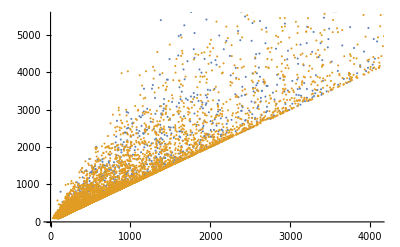

```mathematica
ListPlot[{sbmptn1a,sbmptn1b}]
```

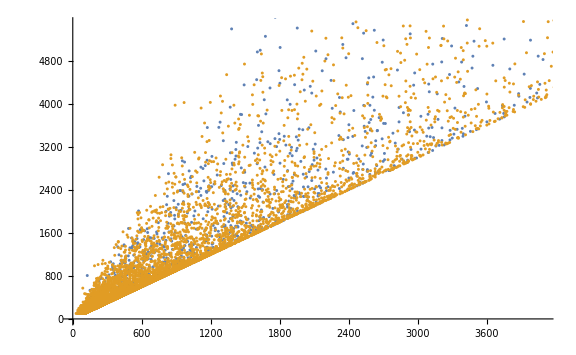

```mathematica
Show[%49,ImageSize->Large]
```

```mathematica
sbmptn =.
```

```mathematica
ClearAll[sbmptn,sbmptn1,sbmptn1a,sbmptn1b]
```

```mathematica
sbmptn = Import["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/logs/mat-class-sbmptn.json"]
```

{{total→391,ratio→432,lulus→False},{total→212,ratio→665,lulus→False},{total→730,ratio→901,lulus→False},{total→218,ratio→853,lulus→False},8391,{total→604,ratio→758,lulus→True},{total→153,ratio→967,lulus→False},{total→245,ratio→1000,lulus→False},{total→1916,ratio→498,lulus→False}}
 |  |  |  |

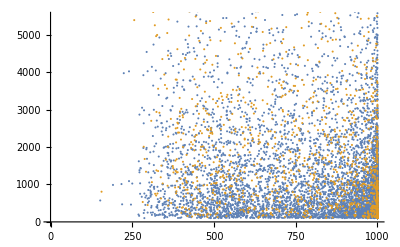

```mathematica
ListPlot[{Map[{Lookup[#,"ratio"],Lookup[#, "total"]}&, Select[sbmptn,Not[Lookup[#,"lulus"]]&]],Map[{Lookup[#,"ratio"], Lookup[#,"total"]}&,Select[sbmptn,Lookup[#,"lulus"]&]]}]
```

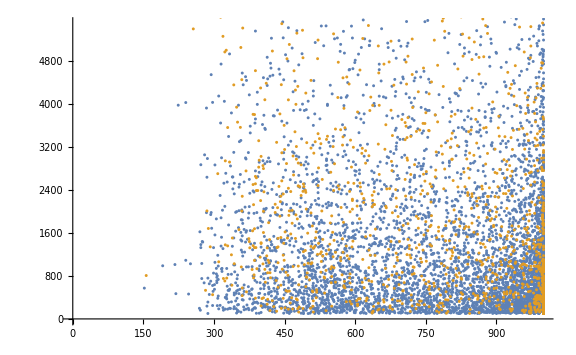

```mathematica
Show[%65,ImageSize->Large]
```

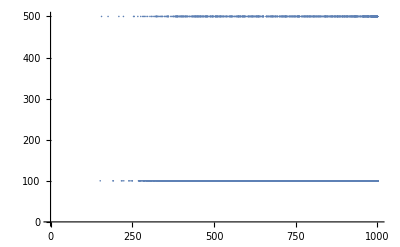

```mathematica
ListPlot[sbmptn]
```